# Generalized QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["QKT.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Grid

```mathematica
radius=2;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

```mathematica
ListPlot[region,AspectRatio->1]
```

## Method

```mathematica
Names["QKT`*"]
```

{Floq,Floqb,Floqbn,Floqn,generateCoherentStateCompiler,generateSpinOperators,MeanLevelSpacingRatio}

```mathematica
(*Floquet parameters*)
J=1000;
d=2 J+1;
α=0.84;
k=20.;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[points]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 0 points...

```mathematica
?Floq
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
sz=ops[[3]];
(*Compute expected values of Sz for each eigenvector*)
szExpectations=Map[#.sz.ConjugateTranspose[#]&,neweigenvec];
(*Get ordering of eigenvectors by increasing<Sz>*)
ordering=Ordering[szExpectations];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.538561,0.533296}

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

-Graphics-

```mathematica
husimiValues=Abs[overlaps]^2;
```

```mathematica
q=-1;
plots=ListDensityPlot[MapThread[Append,{region,husimiValues[[q]]}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q ="<>ToString[q],25,Black],ImageSize->700,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
Export["test.png",plots]
```

test.png

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
(*Set parameters*)
numEigenstates=2J+1; 
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValues[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];;
plot],{q,3}];
```

# Localization measures

```mathematica
info=SortBy[Transpose[{iprCompiled,region,Transpose[overlaps]}],First];
```

```mathematica
newregion=info[[All,2]];
newiprs=info[[All,1]];
newoverlaps=info[[All,3]];
```

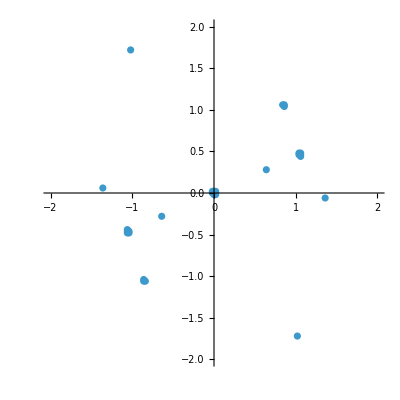

```mathematica
ListPlot[newregion[[-30;;-1]],AspectRatio->1,PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
plots=Table[ListPlot[Transpose[{Arg[eigenvalSorted],Abs[newoverlaps[[i]]]^2}],PlotRange->All,Filling->Bottom,ImageSize->600,PlotLabel->Style["PR = "<>ToString[1/newiprs[[i]]]<>", q = "<>ToString[i],20,Black]],{i,-30,-1,1}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
plots=Table[ListPlot[Transpose[{Arg[eigenvalSorted],Abs[newoverlaps[[i]]]^2}],PlotRange->All,Filling->Bottom,ImageSize->600,PlotLabel->Style["PR = "<>ToString[1/newiprs[[i]]],20,Black]],{i,1,10,1}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

## Searching for Scared eigenvector

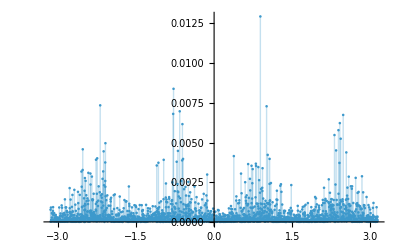

```mathematica
ListPlot[Transpose[{Arg[eigenvalSorted],Abs[newoverlaps[[-28]]]^2}],PlotRange->All,Filling->Bottom]
```

```mathematica
Max[Abs[newoverlaps[[-28]]]^2]
```

0.0129375

```mathematica
Sort[Abs[newoverlaps[[-28]]]^2][[-1]]
```

0.0129375

```mathematica
(*Compute expected values of Sz for each eigenvector*)
szExpectations=Sort[Abs[newoverlaps[[-28]]]^2];
(*Get ordering of eigenvectors by increasing<Sz>*)
ordering=Ordering[szExpectations];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
q=-1;
```